# Числено интегриране. Квадратурни формули на Нютон-Коутс

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
Дадена е функцията f(x) = (b + 2 - x)/(2 x^2+a+1)
1. Табулирайте функцията f(x) в интервала [a, a+b+1], като разделите интервала на b+5 равни части.
2. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
3. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
4. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници, използвайки точките получени в 1. Каква е грешката на полученото приближение?
5. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците, използвайки точките получени в 1. Каква е грешката на полученото приближение?
6. Може ли по построената в 1 таблица да се използва квадратурната формула на Симпсън за изчисляване на интеграла ∫_a^(a+b+1) f(x)ⅆx? Обосновете отговора си. Ако може, го изчислете и пресметнете каква е грешката на полученото приближение?
7. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на левите правоъгълници с точност 0.00001.
8. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на десните правоъгълници с точност 0.00001.
9. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на средните правоъгълници с точност 0.00001.
10. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на трапеците с точност 0.00001.
11. Пресметнете ∫_a^(a+b+1) f(x)ⅆx по формулата на Симпсън с точност 0.00001.

## Съставяне на мрежата

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 14;
h = (b-a)/n;

Print["Мрежата е с брой подинтервали n = ", n, " и стъпка h = ",h]
xt = Table[a + i*h, {i,0,n}]
```

Мрежата е с брой подинтервали n = 14 и стъпка h = 0.785714

{1.,1.78571,2.57143,3.35714,4.14286,4.92857,5.71429,6.5,7.28571,8.07143,8.85714,9.64286,10.4286,11.2143,12.}

```mathematica
f[xt]
```

{2.5,1.09988,0.553619,0.311435,0.188764,0.120032,0.0785324,0.0520231,0.0343396,0.0221365,0.0134857,0.00722002,0.0026032,-0.00084524,-0.00344828}

## Леви правоъгълници

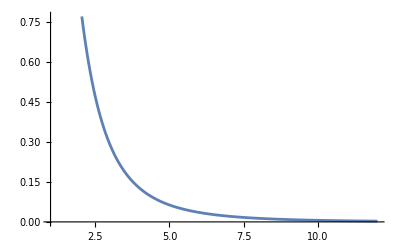

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 14;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.785714 и брой подинтервали 14

Приближената стойност по формулата на левите правоъгълници е 3.91539

Точната стойност                                           е 2.79152

Теоретичната грешка по формулата на левите правоъгълници   е 11.8839

Истинската грешка по формулата на левите правоъгълници     е 1.12387

## Десни правоъгълници

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

-Graphics-

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 14;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на десните правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на десните правоъгълници   е ", R2]
Print["Истинската грешка по формулата на десните правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 0.785714 и брой подинтервали 14

Приближената стойност по формулата на десните правоъгълници е 3.91268

Точната стойност                                           е 2.79152

Теоретичната грешка по формулата на десните правоъгълници   е 11.8839

Истинската грешка по формулата на десните правоъгълници     е 1.12116

## Средни правоъгълници

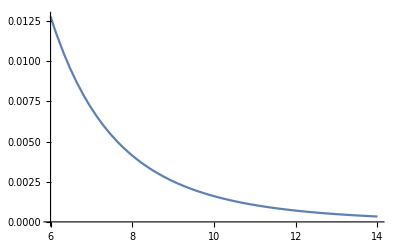

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 14;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на средните правоъгълници е ", I3]
Print["Точната стойност                                             е ", Itochno]
Print["Теоретичната грешка по формулата на средните правоъгълници   е ", R3]
Print["Истинската грешка по формулата на средните правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.785714 и брой подинтервали 14

Приближената стойност по формулата на средните правоъгълници е 2.72173

Точната стойност                                             е 2.79152

Теоретичната грешка по формулата на средните правоъгълници   е 0.848852

Истинската грешка по формулата на средните правоъгълници     е 0.0697817

## Трапеци

```mathematica
Plot[Abs[f''[x]],{x,a,b}]
```

-Graphics-

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 14;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2 = Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.785714 и брой подинтервали 14

Приближената стойност по формулата на трапците е 2.93189

Точната стойност                               е 2.79152

Теоретичната грешка по формулата на трапците   е 1.6977

Истинската грешка по формулата на трапците     е 0.140376

## Симпсън

Може да използваме формулата на Симпсън, тъй като броят на подинтервалите е четно число - в случая 12.

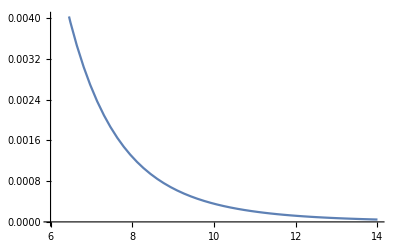

```mathematica
Plot[Abs[f''''[x]],{x,a,b}]
```

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 14;
h = (b-a)/n;

Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.785714 и брой подинтервали 14

Приближената стойност по формулата на Симпсън  е 2.79891

Точната стойност                               е 2.79152

Теоретичната грешка по формулата на Симпсън    е 0.349357

Истинската грешка по формулата на Симпсън      е 0.00739635

# Пресмятане с предварително зададена точност

## Леви правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M1<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.66375×10^7

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 1.664*10^7;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] 
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 6.61058×10^-7 и брой подинтервали 1.664×10^7

Приближената стойност по формулата на левите правоъгълници е 2.79152

Точната стойност                                           е 2.79152

Теоретичната грешка по формулата на левите правоъгълници   е 9.9985×10^-6

Истинската грешка по формулата на левите правоъгълници     е 8.29921×10^-7

## Десни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^2/(2n)*M2<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n<0||n≥1.815×10^7

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 1.82*10^7;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
I2 = h*∑_(i=0)^n f[a+i*h];
M2 = Abs[f'[a]];
R2 = (b-a)^2/(2n)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n] // N
Print["Приближената стойност по формулата на десните правоъгълници е ", I2]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на десните правоъгълници   е ", R2]
Print["Истинската грешка по формулата на десните правоъгълници     е ", Abs[I2-Itochno]]
```

Мрежата е със стъпка 6.04396×10^-7 и брой подинтервали 1.82×10^7

Приближената стойност по формулата на десните правоъгълници е 2.79152

Точната стойност                                           е 2.79152

Теоретичната грешка по формулата на десните правоъгълници   е 9.14148×10^-6

Истинската грешка по формулата на десните правоъгълници     е 7.56911×10^-7

## Средни правоъгълници

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(24 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-4078.91||n≥4078.91

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 4079;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
I3 = h*∑_(i=0)^(n-1) f[a+i*h + h/2];
M3 = Abs[f''[a]];
R3= (b-a)^3/(24 n^2)*M3;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I3]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R3]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I3-Itochno]]
```

Мрежата е със стъпка 0.00269674 и брой подинтервали 4079

Приближената стойност по формулата на левите правоъгълници е 2.79152

Точната стойност                                           е 2.79152

Теоретичната грешка по формулата на левите правоъгълници   е 9.99955×10^-6

Истинската грешка по формулата на левите правоъгълници     е 8.29966×10^-7

## Трапеци

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^3/(12 n^2)*M3<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-5768.45||n≥5768.45

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 5769;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
IT = h/2*(f[a]+2∑_(i=1)^(n-1) f[a+i*h]+f[b]);
M2= Abs[f''[a]];
RT = (b-a)^3/(12 n^2)*M2;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на трапците е ", IT]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на трапците   е ", RT]
Print["Истинската грешка по формулата на трапците     е ", Abs[IT-Itochno]]
```

Мрежата е със стъпка 0.00190674 и брой подинтервали 5769

Приближената стойност по формулата на трапците е 2.79152

Точната стойност                               е 2.79152

Теоретичната грешка по формулата на трапците   е 9.99809×10^-6

Истинската грешка по формулата на трапците     е 8.34761×10^-7

## Симпсън

```mathematica
eps = 10^-5;
Clear[n]
Reduce[(b-a)^5/(180 n^4)*M4<=eps, n]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n≤-191.402||n≥191.402

```mathematica
f[x_]:=(11-x)/(2 x^2 + 2)
a = 1.; b = 12.;
n = 192;
h = (b-a)/n;
Itochno = ∫_a^b f[x]ⅆx ;
m = n /2;
IS = h/3*(f[a]+4∑_(i=1)^m f[a+(2i-1)*h]+2∑_(i=1)^(m-1) f[a+(2i)*h]+f[b]);
M4 = Abs[f''''[a]];
RS = (b-a)^5/(180 n^4)*M4;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на Симпсън  е ", IS]
Print["Точната стойност                               е ", Itochno]
Print["Теоретичната грешка по формулата на Симпсън    е ", RS]
Print["Истинската грешка по формулата на Симпсън      е ", Abs[IS-Itochno]]
```

Мрежата е със стъпка 0.0572917 и брой подинтервали 192

Приближената стойност по формулата на Симпсън  е 2.79152

Точната стойност                               е 2.79152

Теоретичната грешка по формулата на Симпсън    е 9.87591×10^-6

Истинската грешка по формулата на Симпсън      е 4.92546×10^-8